```mathematica
Quit
```

## Survival probability and the location of the risk-maximizing concentration

```mathematica
The probability of survival is of the form 1/(1+f[c])
Derivative of 1/(1+f[c]) is proportional to -f'[c]
```

```mathematica
D[1/(1+f[C]),C]
```

-f'[C]/(1+f[C])^2

### Biocidal antibiotic, density affects birth

```mathematica
Quit
```

```mathematica
f[c_] = (αR[c]+δR)/ρR[c](1+(γ x0)/s[c]);
D[f[c],c]/.{ρR'[c]-> - αR'[c]}//FullSimplify
```

(-x0 γ (δR+αR[c]) ρR[c] s'[c]+s[c] (x0 γ+s[c]) (δR+αR[c]+ρR[c]) αR'[c])/(s[c]^2 ρR[c]^2)

Validation the rewriting in the form of the manuscript (Eq. (C.5))

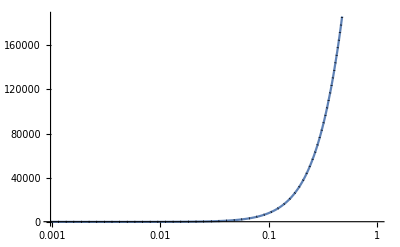

```mathematica
κ = 1.1;
psiMin =-156Log[10];
βS = 2.5;
δS = 0.5;
βR = 2.25;
δR = 0.5;
γ = 1;
x0 = (βS-δS)/γ;
micS = 0.017;
micR =5 micS;
psiMaxS = βS-δS;
psiMaxR = βR-δR;
αS[c_] = (psiMaxS-psiMin)(c/micS)^κ/((c/micS)^κ-psiMin/psiMaxS);
αR[c_] = (psiMaxR-psiMin)(c/micR)^κ/((c/micR)^κ-psiMin/psiMaxR);
f1[c_]= -x0 γ (δR+αR[c]) ρR[c] s'[c]+s[c] (x0 γ+s[c]) (δR+αR[c]+ρR[c]) αR'[c]/.{s'[c]->  D[αS[c],c] - D[αR[c],c],ρR[c]-> βR-δR-αR[c],ρS[c]-> βS-δS-αS[c],s[c]-> βR-δR-αR[c]-βS+δS+αS[c],ρR'[c]-> - D[αR[c],c],ρS'[c]-> - D[αS[c],c]}//FullSimplify ;
f2[c_]= x0 γ ρR[c](δR+αR[c])( D[αR[c],c] - D[αS[c],c])+βR (ρR[c]-ρS[c]) D[αR[c],c](x0 γ+ρR[c]-ρS[c]) /.{s'[c]->  D[αS[c],c] - D[αR[c],c],ρR[c]-> βR-δR-αR[c],ρS[c]-> βS-δS-αS[c],s[c]-> βR-δR-αR[c]-βS+δS+αS[c],ρR'[c]-> - D[αR[c],c],ρS'[c]-> - D[αS[c],c]};
Show[LogLinearPlot[f1[c],{c,0,1}],LogLinearPlot[f2[c],{c,0,1},PlotStyle->{Black,Dotted}]]
```

```mathematica
Quit
```

Solving f' (c) = 0 analytically

```mathematica
Solve[x0 γ ρR[c](δR+αR[c])( D[αR[c],c] - D[αS[c],c])+βR (ρR[c]-ρS[c]) D[αR[c],c](x0 γ+ρR[c]-ρS[c]) == 0,D[αS[c],c]]//FullSimplify
```

{{αS'[c]→((βR ρR[c]^2+βR ρS[c] (-x0 γ+ρS[c])+ρR[c] (x0 γ (βR+δR+αR[c])-2 βR ρS[c])) αR'[c])/(x0 γ (δR+αR[c]) ρR[c])}}

Validating Eq. (C.6)

```mathematica
((βR ρR[c]^2+βR ρS[c] (-x0 γ+ρS[c])+ρR[c] (x0 γ (βR+δR+αR[c])-2 βR ρS[c])) αR'[c])/(x0 γ (δR+αR[c]) ρR[c])- αR'[c](1+(βR(ρR[c]-ρS[c]))/(ρR[c](δR+αR[c]))+(βR(ρR[c]-ρS[c])^2)/(x0 γ ρR[c](δR+αR[c])))//FullSimplify
```

0

#### Numerical exploration

```mathematica
κ = 1.1;
psiMin =-156Log[10];
βS = 2.5;
δS = 0.5;
βR = 2.25;
δR = 0.5;
γ = 1;
x0 = (βS-δS)/γ;
micS = 0.017;
micR =5 micS;
psiMaxS = βS-δS;
psiMaxR = βR-δR;
αS[c_] = (psiMaxS-psiMin)(c/micS)^κ/((c/micS)^κ-psiMin/psiMaxS);
αR[c_] = (psiMaxR-psiMin)(c/micR)^κ/((c/micR)^κ-psiMin/psiMaxR);
```

```mathematica
Evaluation of Eq. (B .13)
```

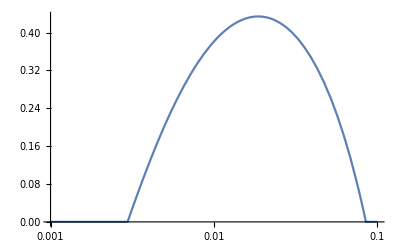

```mathematica
f[c_] = (αR[c]+δR)/ρR[c](1+(γ x0)/s[c]);
LogLinearPlot[Max[0,1/(1+f[c])/.{ρR[c]-> βR-δR-αR[c],ρS[c]-> βS-δS-αS[c],s[c]-> βR-δR-αR[c]-βS+δS+αS[c]}],{c,0.001,0.1}]
```

Evaluation of Eq. (C.5)

```mathematica
D[f[c],c]/.{s'[c]->  D[αS[c],c] - D[αR[c],c],ρR[c]-> βR-δR-αR[c],ρS[c]-> βS-δS-αS[c],s[c]-> βR-δR-αR[c]-βS+δS+αS[c],ρR'[c]-> - D[αR[c],c],ρS'[c]-> - D[αS[c],c]}/.{c-> 0.0186}
D[f[c],c]/.{s'[c]->  D[αS[c],c] - D[αR[c],c],ρR[c]-> βR-δR-αR[c],ρS[c]-> βS-δS-αS[c],s[c]-> βR-δR-αR[c]-βS+δS+αS[c],ρR'[c]-> - D[αR[c],c],ρS'[c]-> - D[αS[c],c]}/.{c-> 0.0187}
```

-0.152595

0.278398

Matching to prediction in Eq. (C.6)

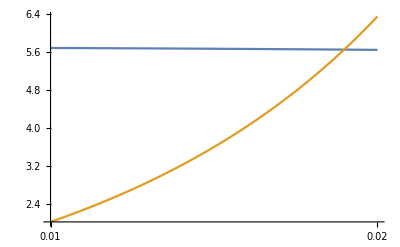

```mathematica
LHS[c_] =D[αS[c],c]/D[αR[c],c]-1;
RHS[c_]=(βR(ρR[c]-ρS[c]))/(ρR[c](δR+αR[c]))+(βR (ρR[c]-ρS[c])^2)/(x0 γ ρR[c](δR+αR[c]))/.{ρR[c]-> βR-δR-αR[c],ρS[c]-> βS-δS-αS[c]};
LogLinearPlot[{LHS[c],RHS[c]},{c,0.01,0.02}]
```

### Biocidal antibiotic, density affects death

```mathematica
Quit
```

```mathematica
f[c_] = (x0 γ (δR+αR[c]+ρS[c]))/(s[c]ρS[c])-((δR+αR[c])(γ x0 - ρS[c]))/(ρS[c] ρR[c]);
D[f[c],c]//FullSimplify
```

(-(x0 γ ρS[c] (δR+αR[c]+ρS[c]) s'[c])/s[c]^2+(x0 γ (ρS[c] αR'[c]-(δR+αR[c]) ρS'[c]))/s[c]+(-(x0 γ-ρS[c]) ρS[c] (ρR[c] αR'[c]-(δR+αR[c]) ρR'[c])+x0 γ (δR+αR[c]) ρR[c] ρS'[c])/ρR[c]^2)/ρS[c]^2

Validation the rewriting in the form of the manuscript (Eq. (C.8))

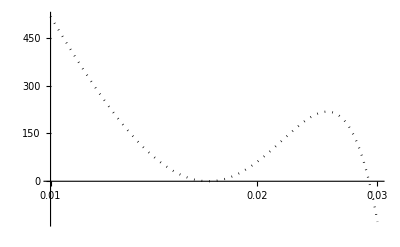

```mathematica
κ = 1.1;
psiMin =-156Log[10];
βS = 2.5;
δS = 0.5;
βR = 2.25;
δR = 0.5;
γ = 1;
x0 = (βS-δS)/γ;
micS = 0.017;
micR =5 micS;
psiMaxS = βS-δS;
psiMaxR = βR-δR;
αS[c_] = (psiMaxS-psiMin)(c/micS)^κ/((c/micS)^κ-psiMin/psiMaxS);
αR[c_] = (psiMaxR-psiMin)(c/micR)^κ/((c/micR)^κ-psiMin/psiMaxR);
f1[c_]= -D[f[c],c]//FullSimplify /.{s'[c]->  D[αS[c],c] - D[αR[c],c],ρR[c]-> βR-δR-αR[c],ρS[c]-> βS-δS-αS[c],s[c]-> βR-δR-αR[c]-βS+δS+αS[c],ρR'[c]-> - D[αR[c],c],ρS'[c]-> - D[αS[c],c]};
f2[c_]=  D[αS[c],c](ρS[c] ρR[c]^2 x0 γ (δR+αR[c]+ρS[c])-x0 γ (ρR[c]-ρS[c])(δR+αR[c])ρS[c]ρR[c])- D[αR[c],c](ρS[c] ρR[c]^2 x0 γ(δR+αR[c]+ρS[c])+ρR[c](ρR[c]-ρS[c])ρS[c]^2(x0 γ+ρR[c]-ρS[c])+ρS[c](ρR[c]-ρS[c])^2 (δR+αR[c])(ρS[c]-x0 γ)) /.{ρR[c]-> βR-δR-αR[c],ρS[c]-> βS-δS-αS[c],s[c]-> βR-δR-αR[c]-βS+δS+αS[c],ρR'[c]-> - D[αR[c],c],ρS'[c]-> - D[αS[c],c]};
Show[LogLinearPlot[f1[c],{c,0.01,0.03}],LogLinearPlot[f2[c],{c,0.01,0.03},PlotStyle->{Black,Dotted}]]
```

```mathematica
Quit
```

Solving f’(c)=0 analytically (Eq. (C.9))

```mathematica
Solve[D[αS[c],c](ρS[c] ρR[c]^2 x0 γ (δR+αR[c]+ρS[c])-x0 γ (ρR[c]-ρS[c])(δR+αR[c])ρS[c]ρR[c])- D[αR[c],c](ρS[c] ρR[c]^2 x0 γ(δR+αR[c]+ρS[c])+ρR[c](ρR[c]-ρS[c])ρS[c]^2(x0 γ+ρR[c]-ρS[c])+ρS[c](ρR[c]-ρS[c])^2 (δR+αR[c])(ρS[c]-x0 γ))== 0,D[αS[c],c]]
```

{{αS'[c]→((2 x0 γ ρR[c]+ρR[c]^2-x0 γ ρS[c]-2 ρR[c] ρS[c]+ρS[c]^2) αR'[c])/(x0 γ ρR[c])}}

#### Numerical exploration

```mathematica
κ = 1.1;
psiMin =-156Log[10];
βS = 2.5;
δS = 0.5;
βR = 2.25;
δR = 0.5;
γ = 1;
x0 = (βS-δS)/γ;
micS = 0.017;
micR =5 micS;
psiMaxS = βS-δS;
psiMaxR = βR-δR;
αS[c_] = (psiMaxS-psiMin)(c/micS)^κ/((c/micS)^κ-psiMin/psiMaxS);
αR[c_] = (psiMaxR-psiMin)(c/micR)^κ/((c/micR)^κ-psiMin/psiMaxR);
```

Evaluation of Eq. (B .13)

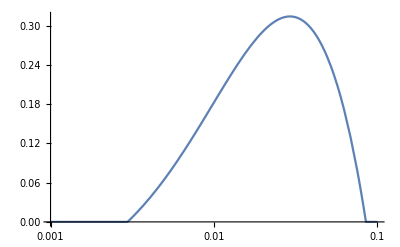

```mathematica
f[c_] = (x0 γ (δR+αR[c]+ρS[c]))/(s[c]ρS[c])-((δR+αR[c])(γ x0 - ρS[c]))/(ρS[c] ρR[c]);
LogLinearPlot[Max[0,1/(1+f[c])/.{ρR[c]-> βR-δR-αR[c],ρS[c]-> βS-δS-αS[c],s[c]-> βR-δR-αR[c]-βS+δS+αS[c]}],{c,0.001,0.1}]
```

Evaluation of Eq. (C.8)

```mathematica
D[f[c],c]/.{s'[c]->  D[αS[c],c] - D[αR[c],c],ρR[c]-> βR-δR-αR[c],ρS[c]-> βS-δS-αS[c],s[c]-> βR-δR-αR[c]-βS+δS+αS[c],ρR'[c]-> - D[αR[c],c],ρS'[c]-> - D[αS[c],c]}/.{c-> 0.029}
D[f[c],c]/.{s'[c]->  D[αS[c],c] - D[αR[c],c],ρR[c]-> βR-δR-αR[c],ρS[c]-> βS-δS-αS[c],s[c]-> βR-δR-αR[c]-βS+δS+αS[c],ρR'[c]-> - D[αR[c],c],ρS'[c]-> - D[αS[c],c]}/.{c-> 0.0295}
```

-0.723571

1.46609

Matching to prediction in Eq. (C.9)

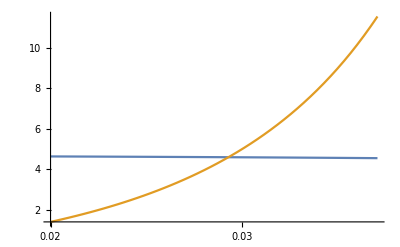

```mathematica
LHS[c_] =D[αS[c],c]/D[αR[c],c]-2;
RHS[c_]=((ρR[c]-ρS[c])^2-x0 γ ρS[c])/(x0 γ ρR[c])/.{ρR[c]-> βR-δR-αR[c],ρS[c]-> βS-δS-αS[c]};
LogLinearPlot[{LHS[c],RHS[c]},{c,0.02,0.04}]
```

### Biostatic antibiotic, density affects death

```mathematica
Quit
```

```mathematica
f[c_] =(x0 γ(δR+ρS[c]))/(ρS[c]s[c])-(δR(γ x0 - ρS[c]))/(ρS[c]ρR[c]);
D[f[c],c]//FullSimplify
```

(ρS[c] (-x0 γ ρR[c]^2 (δR+ρS[c]) s'[c]+δR s[c]^2 (x0 γ-ρS[c]) ρR'[c])+x0 γ δR s[c] (s[c]-ρR[c]) ρR[c] ρS'[c])/(s[c]^2 ρR[c]^2 ρS[c]^2)

Validation the rewriting in the form of the manuscript (Eq. (C.11))

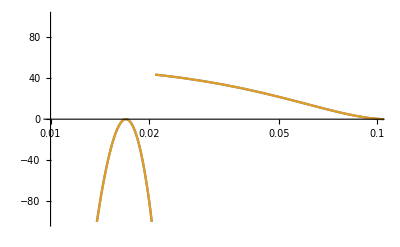

```mathematica
κ = 1.1;
psiMin =-156Log[10];
βS = 2.5;
δS = 0.5;
βR = 2.25;
δR = 0.5;
γ = 1;
x0 = (βS-δS)/γ;
micS = 0.017;
micR =5 micS;
psiMaxS = βS-δS;
psiMaxR = βR-δR;
αS[c_] = (psiMaxS-psiMin)(c/micS)^κ/((c/micS)^κ-psiMin/psiMaxS);
αR[c_] = (psiMaxR-psiMin)(c/micR)^κ/((c/micR)^κ-psiMin/psiMaxR);
f1[c_]=ρS[c] (-x0 γ ρR[c]^2 (δR+ρS[c]) s'[c]+δR s[c]^2 (x0 γ-ρS[c]) ρR'[c])+x0 γ δR s[c] (s[c]-ρR[c]) ρR[c] ρS'[c] /.{s'[c]->  D[Max[βR-αR[c],0],c] - D[Max[βS-αS[c],0],c],ρR[c]-> Max[βR-αR[c],0]-δR,ρS[c]->Max[βS-αS[c],0]-δS,s[c]-> Max[βR-αR[c],0]-δR-(Max[βS-αS[c],0]-δS),ρR'[c]->  D[Max[βR-αR[c],0],c],ρS'[c]->  D[Max[βS-αS[c],0],c]};
f2[c_]=ρS[c](x0 γ ρR[c]^2 (δR+ρS[c])  (D[Max[βS-αS[c],0],c]- D[Max[βR-αR[c],0],c])+δR s[c]^2 (x0 γ-ρS[c])   D[Max[βR-αR[c],0],c] -x0 γ δR s[c]  ρR[c] D[Max[βS-αS[c],0],c])/.{s'[c]->  D[Max[βR-αR[c],0],c] - D[Max[βS-αS[c],0],c],ρR[c]-> Max[βR-αR[c],0]-δR,ρS[c]->Max[βS-αS[c],0]-δS,s[c]-> Max[βR-αR[c],0]-δR-(Max[βS-αS[c],0]-δS),ρR'[c]->  D[Max[βR-αR[c],0],c],ρS'[c]->  D[Max[βS-αS[c],0],c]};
LogLinearPlot[{f1[c],f2[c]},{c,0,1},PlotRange->{{0.01,0.1},{-100,100}}]
```